1/4 (1+x) (17+4 x (1+x))

{{x→1/3 (a+2 b-√((a-b)^2-3 c^2))},{x→1/3 (a+2 b+√((a-b)^2-3 c^2))}}

c^2+(2 a+b-3 x) (b-x)

{{x→1/3 (a+2 b)}}

-a b^2-a c^2+(2 a b+b^2+c^2) x+(-a-2 b) x^2+x^3

-1/3 (a-b)^2+c^2

-2/27 (a-b) ((a-b)^2+9 c^2)

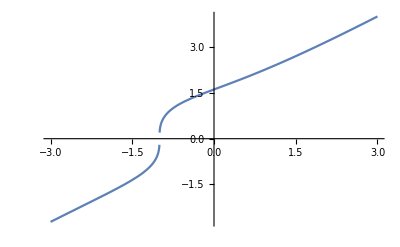

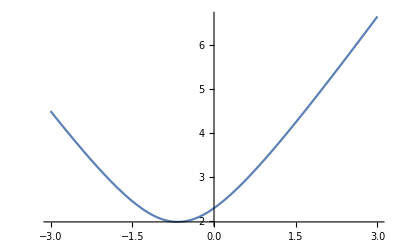

```mathematica
aa=-1;
bb=-1/2;
cc=2;

FullSimplify[Expand[(x-aa)*(x-(bb+I*cc))*(x-(bb-I*cc))]]

ff[x_,a_,b_,c_]:=-(c^2+(b-x)^2) (a-x)
dd[x_,a_,b_,c_]:=c^2+(2 a+b-3 x) (b-x)

FullSimplify[Solve[Collect[dd[x,a,b,c],x]==0,x]]

FullSimplify[D[ff[x,a,b,c],x]]
sol=Solve[FullSimplify[D[ff[x,a,b,c],{x,2}]]==0,x]
Collect[FullSimplify[ff[x,a,b,c]],x]
FullSimplify[D[ff[x,a,b,c],x] /.sol[[1]]]

FullSimplify[ff[x,a,b,c]/.sol[[1]]]

Plot[Sign[ff[x,aa,bb,cc]]*Abs[ff[x,aa,bb,cc]]^(1/3),{x,-3,3}]
Plot[Sign[dd[x,aa,bb,cc]]*Abs[dd[x,aa,bb,cc]]^(1/2),{x,-3,3}]
```